## Biparental invasion of a uniparental population (see Supplemental Material: Maternal transmission as a microbial symbiont sieve, and the absence of lactation in male mammals, Section S1.A)

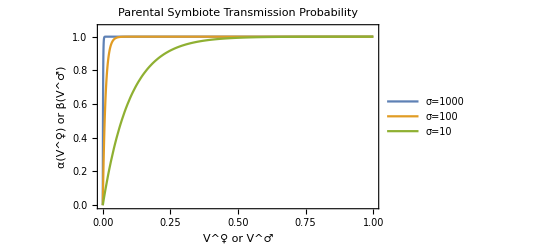

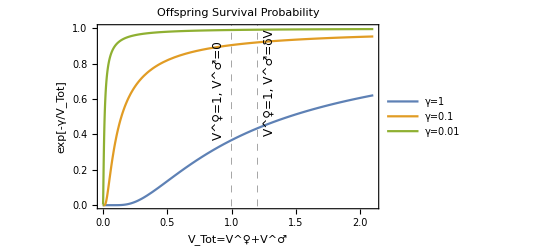

```mathematica
(* Define transmission probability as a function of parental milk volume supplied (see Eqs.(S3-S4)) *)

Plot[Evaluate[((1-Exp[-s*vM])/(1-Exp[-s]))/.{{s->1000},{s->100},{s->10}}],{vM,0,1},PlotRange->{0,1.05},PlotLegends->{Style["σ=1000",15],Style["σ=100",15],Style["σ=10",15]},PlotLabel->Style["Parental Symbiote
Transmission Probability",16],Frame->True,FrameLabel->{Style["V^♀ or V^♂",16],Style["α(V^♀) or β(V^♂)",16]},FrameStyle->16,ImageSize->400]

(* Define offspring survival probability as a function of parental milk volume supplied (see Eqs.(S1-S2)) *)

Plot[Evaluate[(Exp[-γ/vTot])/.{{γ->1},{γ->0.1},{γ->0.01}}],{vTot,0,2.1},PlotRange->{0,1},PlotLegends->{Style["γ=1",15],Style["γ=0.1",15],Style["γ=0.01",15]},PlotLabel->Style["Offspring Survival
Probability",16],Frame->True,FrameLabel->{Style["V_Tot=V^♀+V^♂",16],Style["exp[-γ/V_Tot]",16]},GridLines->{{1,1.2},None},GridLinesStyle->Directive[Thick,Gray, Dashed],Epilog->{Inset[Rotate[Style["V^♀=1, V^♂=0",12],π/2],{0.9,0.65}],Inset[Rotate[Style["V^♀=1, V^♂=δV",12],π/2],{1.3,0.69}]},FrameStyle->16,ImageSize->400]
```

```mathematica
(* Conduct parameter sweep over γ and σ (σ is labelled as s in the following code) *)
```

### γ=0.01, s=1000

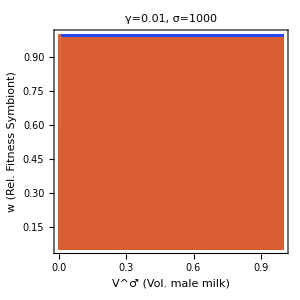

```mathematica
(* Sweep over different biparental male milk volumes, vM, and fitness of hosts carrying the symbiote, w *)

vwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=vwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[vwi=1,vwi≤Length[vwTable],vwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM-> vwTable[[vwi,1]], ϵ ->0.6, 
γ->0.01,s->1000,
w-> vwTable[[vwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at volume 0, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Biparental-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which biparental males are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[3]]==0,system[[4]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleBiNeg->0,maleBiPos->0})),{maleUnNeg>0,maleUnPos>0}],{maleUnNeg,maleUnPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at near their equilibrium abundances (minus some number of mutants) *)
(* maleBiNeg and maleNiPos are at low abundance (representing the number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]== 0.01,
maleBiPos[0]==   0.01,
maleUnNeg[0]==( maleUnNeg/.fp[[Length[fp]]])-0.01 /.params,
maleUnPos[0]== (maleUnPos/.fp[[Length[fp]]])-0.01 /.params,
femaleNeg[0]==  (maleUnNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleUnPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

vwTable[[vwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[vwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[vwTable,ColorFunction->"LightTemperatureMap",InterpolationOrder->0,FrameLabel->{Style["V^♂ (Vol. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"  Fraction
Uniparental
     male"]
```

### γ=0.01, s=100

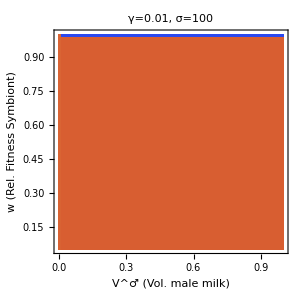

```mathematica
(* Sweep over different biparental male milk volumes, vM, and fitness of hosts carrying the symbiote, w *)

vwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=vwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[vwi=1,vwi≤Length[vwTable],vwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM-> vwTable[[vwi,1]], ϵ ->0.6, 
γ->0.01,s->100,
w-> vwTable[[vwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at volume 0, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Biparental-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which biparental males are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[3]]==0,system[[4]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleBiNeg->0,maleBiPos->0})),{maleUnNeg>0,maleUnPos>0}],{maleUnNeg,maleUnPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at near their equilibrium abundances (minus some number of mutants) *)
(* maleBiNeg and maleNiPos are at low abundance (representing the number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]== 0.01,
maleBiPos[0]==   0.01,
maleUnNeg[0]==( maleUnNeg/.fp[[Length[fp]]])-0.01 /.params,
maleUnPos[0]== (maleUnPos/.fp[[Length[fp]]])-0.01 /.params,
femaleNeg[0]==  (maleUnNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleUnPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

vwTable[[vwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[vwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[vwTable,ColorFunction->"LightTemperatureMap",InterpolationOrder->0,FrameLabel->{Style["V^♂ (Vol. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"  Fraction
Uniparental
     male"]
```

### γ=0.01, s=10

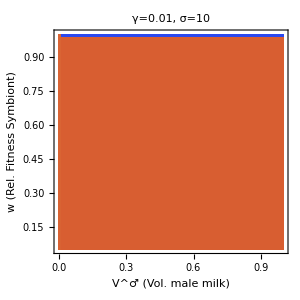

```mathematica
(* Sweep over different biparental male milk volumes, vM, and fitness of hosts carrying the symbiote, w *)

vwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=vwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[vwi=1,vwi≤Length[vwTable],vwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM-> vwTable[[vwi,1]], ϵ ->0.6, 
γ->0.01,s->10,
w-> vwTable[[vwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at volume 0, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Biparental-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which biparental males are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[3]]==0,system[[4]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleBiNeg->0,maleBiPos->0})),{maleUnNeg>0,maleUnPos>0}],{maleUnNeg,maleUnPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at near their equilibrium abundances (minus some number of mutants) *)
(* maleBiNeg and maleNiPos are at low abundance (representing the number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]== 0.01,
maleBiPos[0]==   0.01,
maleUnNeg[0]==( maleUnNeg/.fp[[Length[fp]]])-0.01 /.params,
maleUnPos[0]== (maleUnPos/.fp[[Length[fp]]])-0.01 /.params,
femaleNeg[0]==  (maleUnNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleUnPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

vwTable[[vwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[vwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[vwTable,ColorFunction->"LightTemperatureMap",InterpolationOrder->0,FrameLabel->{Style["V^♂ (Vol. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"  Fraction
Uniparental
     male"]
```

### γ=0.1, s=1000

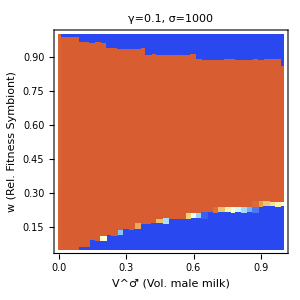

```mathematica
(* Sweep over different biparental male milk volumes, vM, and fitness of hosts carrying the symbiote, w *)

vwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=vwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[vwi=1,vwi≤Length[vwTable],vwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM-> vwTable[[vwi,1]], ϵ ->0.6, 
γ->0.1,s->1000,
w-> vwTable[[vwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at volume 0, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Biparental-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which biparental males are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[3]]==0,system[[4]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleBiNeg->0,maleBiPos->0})),{maleUnNeg>0,maleUnPos>0}],{maleUnNeg,maleUnPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at near their equilibrium abundances (minus some number of mutants) *)
(* maleBiNeg and maleNiPos are at low abundance (representing the number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]== 0.01,
maleBiPos[0]==   0.01,
maleUnNeg[0]==( maleUnNeg/.fp[[Length[fp]]])-0.01 /.params,
maleUnPos[0]== (maleUnPos/.fp[[Length[fp]]])-0.01 /.params,
femaleNeg[0]==  (maleUnNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleUnPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

vwTable[[vwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[vwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[vwTable,ColorFunction->"LightTemperatureMap",InterpolationOrder->0,FrameLabel->{Style["V^♂ (Vol. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"  Fraction
Uniparental
     male"]
```

### γ=0.1, s=100

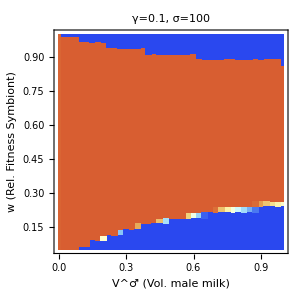

```mathematica
(* Sweep over different biparental male milk volumes, vM, and fitness of hosts carrying the symbiote, w *)

vwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=vwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[vwi=1,vwi≤Length[vwTable],vwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM-> vwTable[[vwi,1]], ϵ ->0.6, 
γ->0.1,s->100,
w-> vwTable[[vwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at volume 0, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Biparental-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which biparental males are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[3]]==0,system[[4]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleBiNeg->0,maleBiPos->0})),{maleUnNeg>0,maleUnPos>0}],{maleUnNeg,maleUnPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at near their equilibrium abundances (minus some number of mutants) *)
(* maleBiNeg and maleNiPos are at low abundance (representing the number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]== 0.01,
maleBiPos[0]==   0.01,
maleUnNeg[0]==( maleUnNeg/.fp[[Length[fp]]])-0.01 /.params,
maleUnPos[0]== (maleUnPos/.fp[[Length[fp]]])-0.01 /.params,
femaleNeg[0]==  (maleUnNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleUnPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

vwTable[[vwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[vwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[vwTable,ColorFunction->"LightTemperatureMap",InterpolationOrder->0,FrameLabel->{Style["V^♂ (Vol. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"  Fraction
Uniparental
     male"]
```

### γ=0.1, s=10

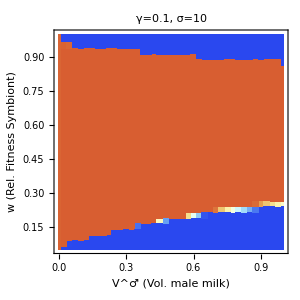

```mathematica
(* Sweep over different biparental male milk volumes, vM, and fitness of hosts carrying the symbiote, w *)

vwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=vwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[vwi=1,vwi≤Length[vwTable],vwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM-> vwTable[[vwi,1]], ϵ ->0.6, 
γ->0.1,s->10,
w-> vwTable[[vwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at volume 0, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Biparental-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which biparental males are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[3]]==0,system[[4]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleBiNeg->0,maleBiPos->0})),{maleUnNeg>0,maleUnPos>0}],{maleUnNeg,maleUnPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at near their equilibrium abundances (minus some number of mutants) *)
(* maleBiNeg and maleNiPos are at low abundance (representing the number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]== 0.01,
maleBiPos[0]==   0.01,
maleUnNeg[0]==( maleUnNeg/.fp[[Length[fp]]])-0.01 /.params,
maleUnPos[0]== (maleUnPos/.fp[[Length[fp]]])-0.01 /.params,
femaleNeg[0]==  (maleUnNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleUnPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

vwTable[[vwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[vwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[vwTable,ColorFunction->"LightTemperatureMap",InterpolationOrder->0,FrameLabel->{Style["V^♂ (Vol. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"  Fraction
Uniparental
     male"]
```

### γ=1, s=1000

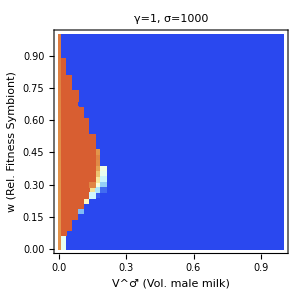

```mathematica
(* Sweep over different biparental male milk volumes, vM, and fitness of hosts carrying the symbiote, w *)

vwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=vwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[vwi=1,vwi≤Length[vwTable],vwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM-> vwTable[[vwi,1]], ϵ ->0.6, 
γ->1,s->1000,
w-> vwTable[[vwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at volume 0, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Biparental-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which biparental males are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[3]]==0,system[[4]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleBiNeg->0,maleBiPos->0})),{maleUnNeg>0,maleUnPos>0}],{maleUnNeg,maleUnPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at near their equilibrium abundances (minus some number of mutants) *)
(* maleBiNeg and maleNiPos are at low abundance (representing the number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]== 0.01,
maleBiPos[0]==   0.01,
maleUnNeg[0]==( maleUnNeg/.fp[[Length[fp]]])-0.01 /.params,
maleUnPos[0]== (maleUnPos/.fp[[Length[fp]]])-0.01 /.params,
femaleNeg[0]==  (maleUnNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleUnPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

vwTable[[vwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[vwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[vwTable,
PlotRange->{Automatic,Automatic,All},ColorFunctionScaling->False,ColorFunction->(ColorData["LightTemperatureMap"][Rescale[#,{0,1}]]&),InterpolationOrder->0,FrameLabel->{Style["V^♂ (Vol. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]


BarLegend["LightTemperatureMap",LegendLabel->"  Fraction
Uniparental
     male"]
```

### γ=1, s=100

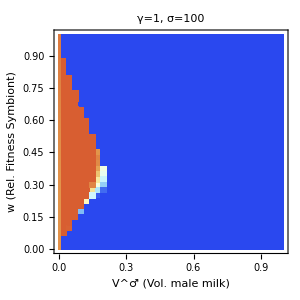

```mathematica
(* Sweep over different biparental male milk volumes, vM, and fitness of hosts carrying the symbiote, w *)

vwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=vwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[vwi=1,vwi≤Length[vwTable],vwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM-> vwTable[[vwi,1]], ϵ ->0.6, 
γ->1,s->100,
w-> vwTable[[vwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at volume 0, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Biparental-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which biparental males are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[3]]==0,system[[4]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleBiNeg->0,maleBiPos->0})),{maleUnNeg>0,maleUnPos>0}],{maleUnNeg,maleUnPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at near their equilibrium abundances (minus some number of mutants) *)
(* maleBiNeg and maleNiPos are at low abundance (representing the number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]== 0.01,
maleBiPos[0]==   0.01,
maleUnNeg[0]==( maleUnNeg/.fp[[Length[fp]]])-0.01 /.params,
maleUnPos[0]== (maleUnPos/.fp[[Length[fp]]])-0.01 /.params,
femaleNeg[0]==  (maleUnNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleUnPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

vwTable[[vwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[vwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[vwTable,
PlotRange->{Automatic,Automatic,All},ColorFunctionScaling->False,ColorFunction->(ColorData["LightTemperatureMap"][Rescale[#,{0,1}]]&),InterpolationOrder->0,FrameLabel->{Style["V^♂ (Vol. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"  Fraction
Uniparental
     male"]
```

### γ=1, s=10

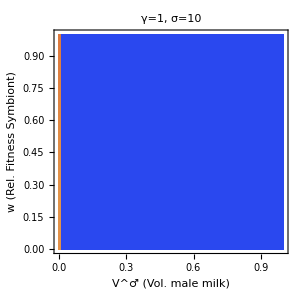

```mathematica
(* Sweep over different biparental male milk volumes, vM, and fitness of hosts carrying the symbiote, w *)

vwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=vwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[vwi=1,vwi≤Length[vwTable],vwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM-> vwTable[[vwi,1]], ϵ ->0.6, 
γ->1,s->10,
w-> vwTable[[vwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at volume 0, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+0)] * (α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[0])femaleNeg*maleUnPos+(1-α[vF])(1-β[0])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+0)](α[vF]maleUnNeg femalePos + β[0]maleUnPos*femaleNeg + (α[vF]+β[0]-α[vF]*β[0])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Biparental-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which biparental males are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[3]]==0,system[[4]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleBiNeg->0,maleBiPos->0})),{maleUnNeg>0,maleUnPos>0}],{maleUnNeg,maleUnPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at near their equilibrium abundances (minus some number of mutants) *)
(* maleBiNeg and maleNiPos are at low abundance (representing the number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]== 0.01,
maleBiPos[0]==   0.01,
maleUnNeg[0]==( maleUnNeg/.fp[[Length[fp]]])-0.01 /.params,
maleUnPos[0]== (maleUnPos/.fp[[Length[fp]]])-0.01 /.params,
femaleNeg[0]==  (maleUnNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleUnPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

vwTable[[vwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[vwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[vwTable,
PlotRange->{Automatic,Automatic,All},ColorFunctionScaling->False,ColorFunction->(ColorData["LightTemperatureMap"][Rescale[#,{0,1}]]&),InterpolationOrder->0,FrameLabel->{Style["V^♂ (Vol. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"  Fraction
Uniparental
     male"]
```

## Invasion of males lactating with a reduced milk volume in a biparental population (see Supplemental Material: Maternal transmission as a microbial symbiont sieve, and the absence of lactation in male mammals, Section S1.B)

```mathematica
(* Define transmission probability as a function of parental milk volume supplied (see Eqs.(S3-S4)) *)

Plot[Evaluate[((1-Exp[-s*vM])/(1-Exp[-s]))/.{{s->1000},{s->100},{s->10}}],{vM,0,1},PlotRange->{0,1.05},PlotLegends->{Style["σ=1000",15],Style["σ=100",15],Style["σ=10",15]},PlotLabel->Style["Parental Symbiote
Transmission Probability",16],Frame->True,FrameLabel->{Style["V^♀ or V^♂",16],Style["α(V^♀) or β(V^♂)",16]},FrameStyle->16,ImageSize->400]

(* Define offspring survival probability as a function of parental milk volume supplied (see Eqs.(S1-S2)) *)

Plot[Evaluate[(Exp[-γ/vTot])/.{{γ->1},{γ->0.1},{γ->0.01}}],{vTot,0,2.1},PlotRange->{0,1},PlotLegends->{Style["γ=1",15],Style["γ=0.1",15],Style["γ=0.01",15]},PlotLabel->Style["Offspring Survival
Probability",16],Frame->True,FrameLabel->{Style["V_Tot=V^♀+V^♂",16],Style["exp[-γ/V_Tot]",16]},GridLines->{{1,1.2},None},GridLinesStyle->Directive[Thick,Gray, Dashed],Epilog->{Inset[Rotate[Style["V^♀=1, V^♂=0",12],π/2],{0.9,0.65}],Inset[Rotate[Style["V^♀=1, V^♂=δV",12],π/2],{1.3,0.69}]},FrameStyle->16,ImageSize->400]
```

-Graphics-

-Graphics-

### γ=0.01, s=1000

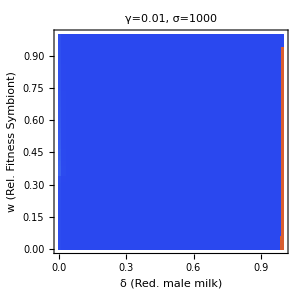

```mathematica
(* Sweep over different reduction in biparental male milk volumes, δ, and fitness of hosts carrying the symbiote, w *)

δwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=δwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[δwi=1,δwi≤Length[δwTable],δwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM->1,
δ-> δwTable[[δwi,1]],
ϵ ->0.6, 
γ->0.01,s->1000,
w-> δwTable[[δwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at reduced volume vM-δ, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at full volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Reduced-lactation-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which males with lower lactation are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[1]]==0,system[[2]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleUnNeg->0,maleUnPos->0})),{maleBiNeg>0,maleBiPos>0}],{maleBiNeg,maleBiPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at low abundance (representing the number of mutants) *)
(* maleBiNeg and maleNiPos are at near their equilibrium abundances (minus some number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]==( maleBiNeg/.fp[[Length[fp]]])-0.01 /.params,
maleBiPos[0]==(maleBiPos/.fp[[Length[fp]]])-0.01 /.params,
maleUnNeg[0]==0.01,
maleUnPos[0]==0.01,
femaleNeg[0]==  (maleBiNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleBiPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

δwTable[[δwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[δwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[δwTable,
PlotRange->{Automatic,Automatic,All},ColorFunctionScaling->False,ColorFunction->(ColorData["LightTemperatureMap"][Rescale[#,{0,1}]]&),InterpolationOrder->0,FrameLabel->{Style["δ (Red. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"    Fraction
 males with 
reduced lact."]
```

### γ=0.01, s=100

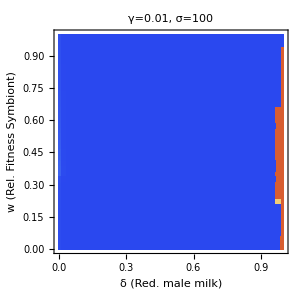

```mathematica
(* Sweep over different reduction in biparental male milk volumes, δ, and fitness of hosts carrying the symbiote, w *)

δwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=δwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[δwi=1,δwi≤Length[δwTable],δwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM->1,
δ-> δwTable[[δwi,1]],
ϵ ->0.6, 
γ->0.01,s->100,
w-> δwTable[[δwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at reduced volume vM-δ, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at full volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Reduced-lactation-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which males with lower lactation are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[1]]==0,system[[2]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleUnNeg->0,maleUnPos->0})),{maleBiNeg>0,maleBiPos>0}],{maleBiNeg,maleBiPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at low abundance (representing the number of mutants) *)
(* maleBiNeg and maleNiPos are at near their equilibrium abundances (minus some number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]==( maleBiNeg/.fp[[Length[fp]]])-0.01 /.params,
maleBiPos[0]==(maleBiPos/.fp[[Length[fp]]])-0.01 /.params,
maleUnNeg[0]==0.01,
maleUnPos[0]==0.01,
femaleNeg[0]==  (maleBiNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleBiPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

δwTable[[δwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[δwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[δwTable,
PlotRange->{Automatic,Automatic,All},ColorFunctionScaling->False,ColorFunction->(ColorData["LightTemperatureMap"][Rescale[#,{0,1}]]&),InterpolationOrder->0,FrameLabel->{Style["δ (Red. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"    Fraction
 males with 
reduced lact."]
```

### γ=0.01, s=10

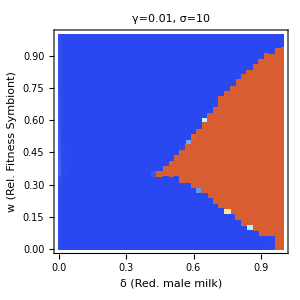

```mathematica
(* Sweep over different reduction in biparental male milk volumes, δ, and fitness of hosts carrying the symbiote, w *)

δwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=δwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[δwi=1,δwi≤Length[δwTable],δwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM->1,
δ-> δwTable[[δwi,1]],
ϵ ->0.6, 
γ->0.01,s->10,
w-> δwTable[[δwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at reduced volume vM-δ, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at full volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Reduced-lactation-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which males with lower lactation are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[1]]==0,system[[2]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleUnNeg->0,maleUnPos->0})),{maleBiNeg>0,maleBiPos>0}],{maleBiNeg,maleBiPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at low abundance (representing the number of mutants) *)
(* maleBiNeg and maleNiPos are at near their equilibrium abundances (minus some number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]==( maleBiNeg/.fp[[Length[fp]]])-0.01 /.params,
maleBiPos[0]==(maleBiPos/.fp[[Length[fp]]])-0.01 /.params,
maleUnNeg[0]==0.01,
maleUnPos[0]==0.01,
femaleNeg[0]==  (maleBiNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleBiPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

δwTable[[δwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[δwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[δwTable,
PlotRange->{Automatic,Automatic,All},ColorFunctionScaling->False,ColorFunction->(ColorData["LightTemperatureMap"][Rescale[#,{0,1}]]&),InterpolationOrder->0,FrameLabel->{Style["δ (Red. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"    Fraction
 males with 
reduced lact."]
```

### γ=0.1, s=1000

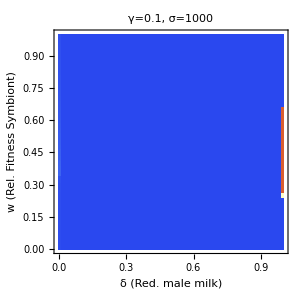

```mathematica
(* Sweep over different reduction in biparental male milk volumes, δ, and fitness of hosts carrying the symbiote, w *)

δwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=δwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[δwi=1,δwi≤Length[δwTable],δwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM->1,
δ-> δwTable[[δwi,1]],
ϵ ->0.6, 
γ->0.1,s->1000,
w-> δwTable[[δwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at reduced volume vM-δ, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at full volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Reduced-lactation-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which males with lower lactation are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[1]]==0,system[[2]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleUnNeg->0,maleUnPos->0})),{maleBiNeg>0,maleBiPos>0}],{maleBiNeg,maleBiPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at low abundance (representing the number of mutants) *)
(* maleBiNeg and maleNiPos are at near their equilibrium abundances (minus some number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]==( maleBiNeg/.fp[[Length[fp]]])-0.01 /.params,
maleBiPos[0]==(maleBiPos/.fp[[Length[fp]]])-0.01 /.params,
maleUnNeg[0]==0.01,
maleUnPos[0]==0.01,
femaleNeg[0]==  (maleBiNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleBiPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

δwTable[[δwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[δwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[δwTable,
PlotRange->{Automatic,Automatic,All},ColorFunctionScaling->False,ColorFunction->(ColorData["LightTemperatureMap"][Rescale[#,{0,1}]]&),InterpolationOrder->0,FrameLabel->{Style["δ (Red. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"    Fraction
 males with 
reduced lact."]
```

### γ=0.1, s=100

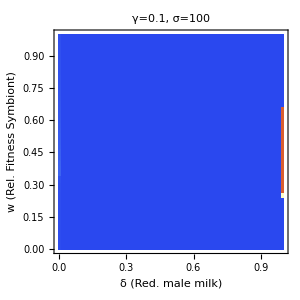

```mathematica
(* Sweep over different reduction in biparental male milk volumes, δ, and fitness of hosts carrying the symbiote, w *)

δwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=δwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[δwi=1,δwi≤Length[δwTable],δwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM->1,
δ-> δwTable[[δwi,1]],
ϵ ->0.6, 
γ->0.1,s->100,
w-> δwTable[[δwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at reduced volume vM-δ, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at full volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Reduced-lactation-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which males with lower lactation are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[1]]==0,system[[2]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleUnNeg->0,maleUnPos->0})),{maleBiNeg>0,maleBiPos>0}],{maleBiNeg,maleBiPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at low abundance (representing the number of mutants) *)
(* maleBiNeg and maleNiPos are at near their equilibrium abundances (minus some number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]==( maleBiNeg/.fp[[Length[fp]]])-0.01 /.params,
maleBiPos[0]==(maleBiPos/.fp[[Length[fp]]])-0.01 /.params,
maleUnNeg[0]==0.01,
maleUnPos[0]==0.01,
femaleNeg[0]==  (maleBiNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleBiPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

δwTable[[δwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[δwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[δwTable,
PlotRange->{Automatic,Automatic,All},ColorFunctionScaling->False,ColorFunction->(ColorData["LightTemperatureMap"][Rescale[#,{0,1}]]&),InterpolationOrder->0,FrameLabel->{Style["δ (Red. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"    Fraction
 males with 
reduced lact."]
```

### γ=0.1, s=10

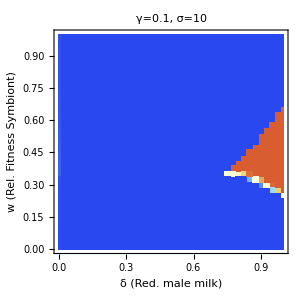

```mathematica
(* Sweep over different reduction in biparental male milk volumes, δ, and fitness of hosts carrying the symbiote, w *)

δwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=δwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[δwi=1,δwi≤Length[δwTable],δwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM->1,
δ-> δwTable[[δwi,1]],
ϵ ->0.6, 
γ->0.1,s->10,
w-> δwTable[[δwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at reduced volume vM-δ, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at full volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Reduced-lactation-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which males with lower lactation are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[1]]==0,system[[2]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleUnNeg->0,maleUnPos->0})),{maleBiNeg>0,maleBiPos>0}],{maleBiNeg,maleBiPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at low abundance (representing the number of mutants) *)
(* maleBiNeg and maleNiPos are at near their equilibrium abundances (minus some number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]==( maleBiNeg/.fp[[Length[fp]]])-0.01 /.params,
maleBiPos[0]==(maleBiPos/.fp[[Length[fp]]])-0.01 /.params,
maleUnNeg[0]==0.01,
maleUnPos[0]==0.01,
femaleNeg[0]==  (maleBiNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleBiPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

δwTable[[δwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[δwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[δwTable,
PlotRange->{Automatic,Automatic,All},ColorFunctionScaling->False,ColorFunction->(ColorData["LightTemperatureMap"][Rescale[#,{0,1}]]&),InterpolationOrder->0,FrameLabel->{Style["δ (Red. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"    Fraction
 males with 
reduced lact."]
```

### γ=1, s=1000

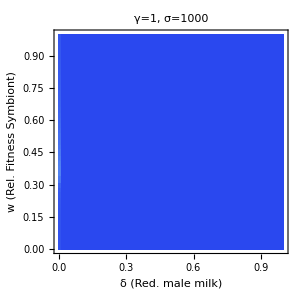

```mathematica
(* Sweep over different reduction in biparental male milk volumes, δ, and fitness of hosts carrying the symbiote, w *)

δwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=δwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[δwi=1,δwi≤Length[δwTable],δwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM->1,
δ-> δwTable[[δwi,1]],
ϵ ->0.6, 
γ->1,s->1000,
w-> δwTable[[δwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at reduced volume vM-δ, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at full volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Reduced-lactation-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which males with lower lactation are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[1]]==0,system[[2]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleUnNeg->0,maleUnPos->0})),{maleBiNeg>0,maleBiPos>0}],{maleBiNeg,maleBiPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at low abundance (representing the number of mutants) *)
(* maleBiNeg and maleNiPos are at near their equilibrium abundances (minus some number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]==( maleBiNeg/.fp[[Length[fp]]])-0.01 /.params,
maleBiPos[0]==(maleBiPos/.fp[[Length[fp]]])-0.01 /.params,
maleUnNeg[0]==0.01,
maleUnPos[0]==0.01,
femaleNeg[0]==  (maleBiNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleBiPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

δwTable[[δwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[δwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[δwTable,
PlotRange->{Automatic,Automatic,All},ColorFunctionScaling->False,ColorFunction->(ColorData["LightTemperatureMap"][Rescale[#,{0,1}]]&),InterpolationOrder->0,FrameLabel->{Style["δ (Red. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"    Fraction
 males with 
reduced lact."]
```

### γ=1, s=100

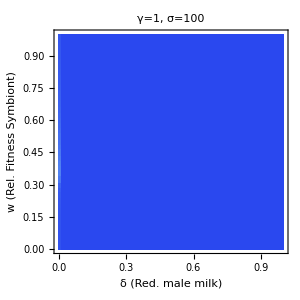

```mathematica
(* Sweep over different reduction in biparental male milk volumes, δ, and fitness of hosts carrying the symbiote, w *)

δwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=δwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[δwi=1,δwi≤Length[δwTable],δwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM->1,
δ-> δwTable[[δwi,1]],
ϵ ->0.6, 
γ->1,s->100,
w-> δwTable[[δwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at reduced volume vM-δ, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at full volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Reduced-lactation-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which males with lower lactation are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[1]]==0,system[[2]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleUnNeg->0,maleUnPos->0})),{maleBiNeg>0,maleBiPos>0}],{maleBiNeg,maleBiPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at low abundance (representing the number of mutants) *)
(* maleBiNeg and maleNiPos are at near their equilibrium abundances (minus some number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]==( maleBiNeg/.fp[[Length[fp]]])-0.01 /.params,
maleBiPos[0]==(maleBiPos/.fp[[Length[fp]]])-0.01 /.params,
maleUnNeg[0]==0.01,
maleUnPos[0]==0.01,
femaleNeg[0]==  (maleBiNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleBiPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

δwTable[[δwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[δwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[δwTable,
PlotRange->{Automatic,Automatic,All},ColorFunctionScaling->False,ColorFunction->(ColorData["LightTemperatureMap"][Rescale[#,{0,1}]]&),InterpolationOrder->0,FrameLabel->{Style["δ (Red. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"    Fraction
 males with 
reduced lact."]
```

### γ=1, s=10

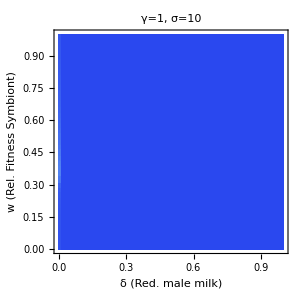

```mathematica
(* Sweep over different reduction in biparental male milk volumes, δ, and fitness of hosts carrying the symbiote, w *)

δwTable=Flatten[Table[{i,j,0},{i,0,1,0.025},{j,0.05,1,0.025}],1];
fpTable=δwTable;

(* Define α and β transmission probability functions *)
α[vF_]:=((1-Exp[-s*vF])/(1-Exp[-s]));
β[vM_]:=((1-Exp[-s*vM])/(1-Exp[-s]));


For[δwi=1,δwi≤Length[δwTable],δwi++,

(* Define fixed parameters in simulation and parameters to vary (vM and w) *)
params={b0 -> 10, d0 -> 1, dprime -> 1/1000, v ->1000,
vF->1,
vM->1,
δ-> δwTable[[δwi,1]],
ϵ ->0.6, 
γ->1,s->10,
w-> δwTable[[δwi,2]],tt->10000};

(* Create RHS of Dynamical System  with ... *)
(* Females lactating at volume vF, with and without symbiote, femalePos and femaleNeg respectively *)
(* Males lactating at reduced volume vM-δ, with and without symbiote, maleUnPos and maleUnNeg respectively *)
(* Males lactating at full volume vM, with and without symbiote, maleBiPos and maleBiNeg respectively *)
system = {
(*d maleBiNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) - maleBiNeg(d0 + dprime v (total)) / 1 - ϵ maleBiNeg+ϵ maleBiPos,

(*d maleBiPos / dt := *)
b0/2 * Exp[-γ/(vF+vM)] * (α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) - maleBiPos(d0 + dprime v (total)) / w + ϵ maleBiNeg - ϵ maleBiPos,

(*d maleUnNeg / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos) - maleUnNeg(d0 + dprime v (total)) / 1 - ϵ maleUnNeg+ϵ maleUnPos,

(*d maleUnPos / dt := *)
b0/2 * Exp[-γ/(vF+vM-δ)] * (α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos) - maleUnPos(d0 + dprime v (total)) / w + ϵ maleUnNeg-ϵ maleUnPos,

(*d femaleNeg / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](maleBiNeg femaleNeg+(1-α[vF])femalePos*maleBiNeg+(1-β[vM])femaleNeg*maleBiPos+(1-α[vF])(1-β[vM])femalePos*maleBiPos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](maleUnNeg femaleNeg+(1-α[vF])femalePos*maleUnNeg+(1-β[vM-δ])femaleNeg*maleUnPos+(1-α[vF])(1-β[vM-δ])femalePos*maleUnPos)/(femaleNeg + femalePos)) - femaleNeg(d0 + dprime v (total)) / 1 - ϵ femaleNeg+ϵ*femalePos,

(*d femalePos / dt := *)
b0/2  * (Exp[-γ/(vF+vM)](α[vF]maleBiNeg femalePos + β[vM]maleBiPos*femaleNeg + (α[vF]+β[vM]-α[vF]*β[vM])maleBiPos*femalePos)/(femaleNeg + femalePos) +  Exp[-γ/(vF+vM-δ)](α[vF]maleUnNeg femalePos + β[vM-δ]maleUnPos*femaleNeg + (α[vF]+β[vM-δ]-α[vF]*β[vM-δ])maleUnPos*femalePos)/(femaleNeg + femalePos)) - femalePos(d0 + dprime v (total)) / w + ϵ femaleNeg - ϵ*femalePos
}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)}/.params;


(* Calculate FP at Reduced-lactation-free Equilibrium using fisherian sex ratios *)
(* This equilibrium forms the initial condition for the population, to which males with lower lactation are introduced at low frequency *)
fp=Quiet[Solve[Join[((({system[[1]]==0,system[[2]]==0}/.{total-> (maleBiNeg+maleBiPos+maleUnNeg+maleUnPos+femaleNeg+femalePos)})/.{femaleNeg->maleBiNeg+maleUnNeg,femalePos->maleBiPos+maleUnPos}/.{maleUnNeg->0,maleUnPos->0})),{maleBiNeg>0,maleBiPos>0}],{maleBiNeg,maleBiPos},Reals]];

(* Check the number of internal equilbria *)
If[Length[fp]>1,Print["Too Many FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
If[Length[fp]==0,Print["Too Few FP: params VM="<>ToString[vM/.params]<>"; w="<>ToString[w/.params]]];
fpNum=fp/.params;

(*Solve for fixed points.*)
subs = {
maleBiNeg -> maleBiNeg [t],maleBiPos-> maleBiPos [t],maleUnNeg-> maleUnNeg [t],maleUnPos-> maleUnPos [t],femaleNeg-> femaleNeg [t],femalePos-> femalePos [t]
};

(* Solve the dynamical system under the assumption that ... *)
(* femaleNeg and femalePos are at their equilibrium abundances *)
(* maleUnNeg and maleUnPos are at low abundance (representing the number of mutants) *)
(* maleBiNeg and maleNiPos are at near their equilibrium abundances (minus some number of mutants) *)
solved = NDSolve[{
maleBiNeg'[t]==(system[[1]]/.subs),
maleBiPos'[t]==(system[[2]]/.subs),
maleUnNeg'[t]==(system[[3]]/.subs),
maleUnPos'[t]==(system[[4]]/.subs),
femaleNeg'[t]==(system[[5]]/.subs),
femalePos'[t]==(system[[6]]/.subs),
maleBiNeg[0]==( maleBiNeg/.fp[[Length[fp]]])-0.01 /.params,
maleBiPos[0]==(maleBiPos/.fp[[Length[fp]]])-0.01 /.params,
maleUnNeg[0]==0.01,
maleUnPos[0]==0.01,
femaleNeg[0]==  (maleBiNeg/.fp[[Length[fp]]]) /.params,
femalePos[0]==(  maleBiPos/.fp[[Length[fp]]]) /.params
}, {
maleBiNeg,maleBiPos,maleUnNeg,maleUnPos,femaleNeg,femalePos
}, {t, 0, tt/.params}];

δwTable[[δwi,3]]=(maleUnNeg[t]+maleUnPos[t])/((maleBiNeg[t]+maleBiPos[t])+(maleUnNeg[t]+maleUnPos[t]))/.solved[[1]]/.t->tt/.params;
fpTable[[δwi,3]]=fp[[Length[fp]]];
]

ListDensityPlot[δwTable,
PlotRange->{Automatic,Automatic,All},ColorFunctionScaling->False,ColorFunction->(ColorData["LightTemperatureMap"][Rescale[#,{0,1}]]&),InterpolationOrder->0,FrameLabel->{Style["δ (Red. male milk)",16],Style["w (Rel. Fitness Symbiont)",16]},PlotLabel->Style["γ="<>ToString[γ/.params]<>", σ="<>ToString[s/.params],18],FrameStyle->14,ImageSize->300]

BarLegend["LightTemperatureMap",LegendLabel->"    Fraction
 males with 
reduced lact."]
```